```mathematica
dir = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS COMPUTACIONAIS C/metcompc/Aula1_2908/Results/";
```

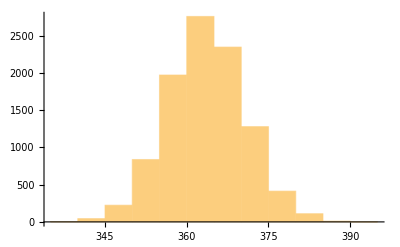

```mathematica
data1 = Import[StringJoin[dir, "CNumberOfDisksPlaced.txt"], "Data"];
Histogram[Flatten[data1]]
```

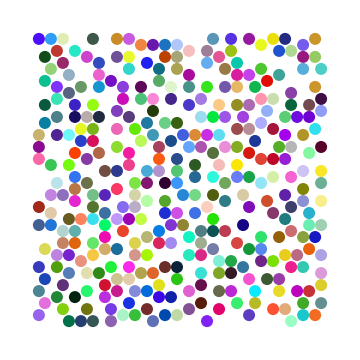
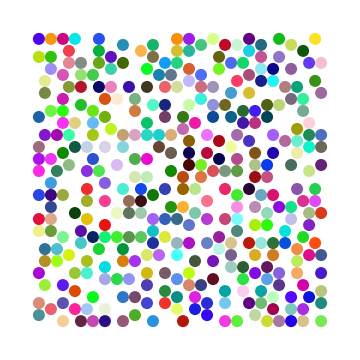
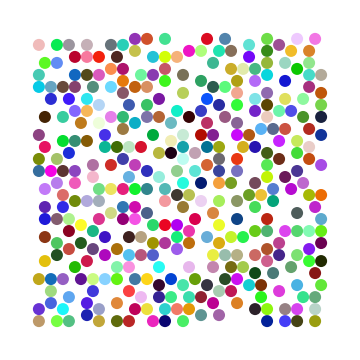
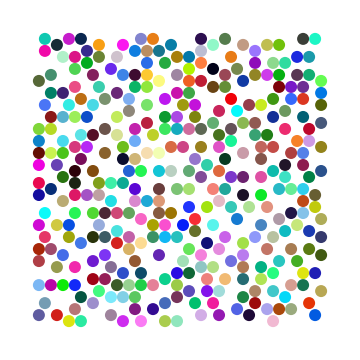

```mathematica
data2 = Table[Import[StringJoin[dir, ToString[StringForm["CPositionsOfDisksPlaced``.txt",i]]], "Data"],{i, 1,4,1}];
Table[Graphics[ Table[Style[Disk[data2[[i]][[j]], 1],RandomColor[]],{j, 1, Length[data2[[i]]], 1}], ImageSize->Medium],{i, 1, 4, 1}]
```

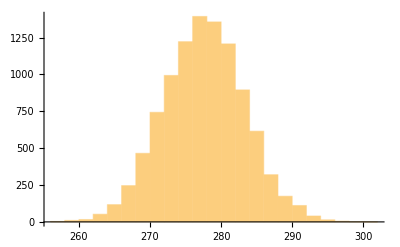

```mathematica
data1Faster = Import[StringJoin[dir, "CNumberOfDisksPlacedFaster.txt"], "Data"];
Histogram[Flatten[data1Faster]]
```

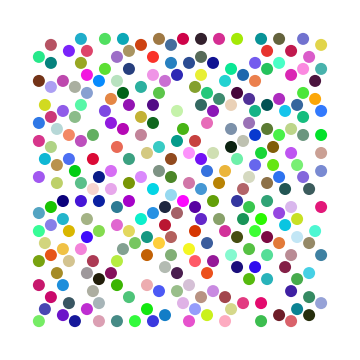
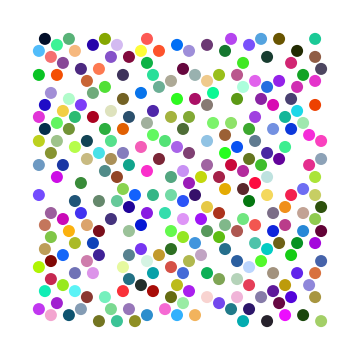
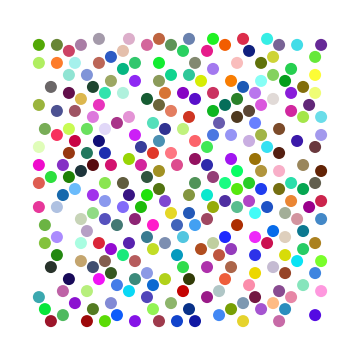
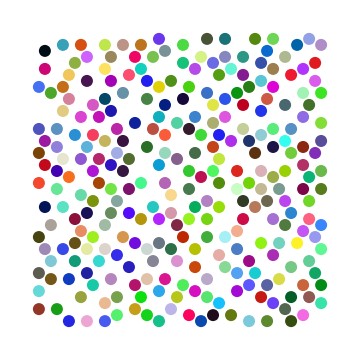

```mathematica
data2Faster = Table[Import[StringJoin[dir, ToString[StringForm["CPositionsOfDisksPlaced``Faster.txt",i]]], "Data"],{i, 1,4,1}];
Table[Graphics[ Table[Style[Disk[data2Faster[[i]][[j]], 1],RandomColor[]],{j, 1, Length[data2Faster[[i]]], 1}], ImageSize->Medium],{i, 1, 4, 1}]
```